{{x→InterpolatingFunction[{{0., 20.}}, <>],y→InterpolatingFunction[{{0., 20.}}, <>],ψ→InterpolatingFunction[{{0., 20.}}, <>],e_ψ→InterpolatingFunction[{{0., 20.}}, <>],e_y→InterpolatingFunction[{{0., 20.}}, <>]}}

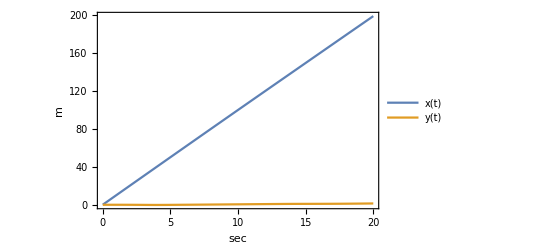

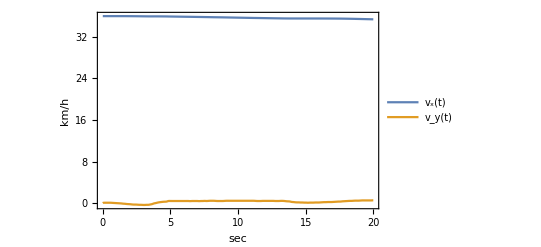

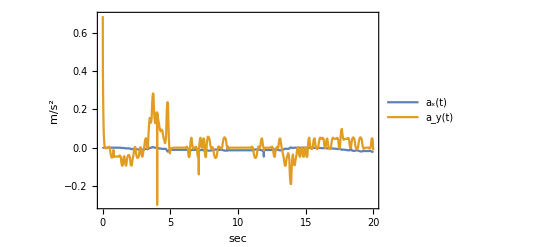

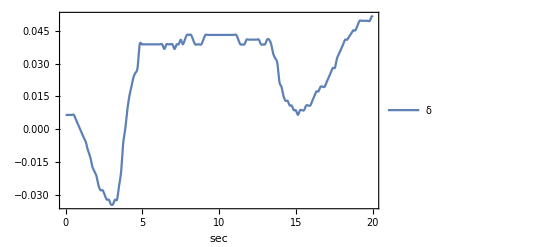

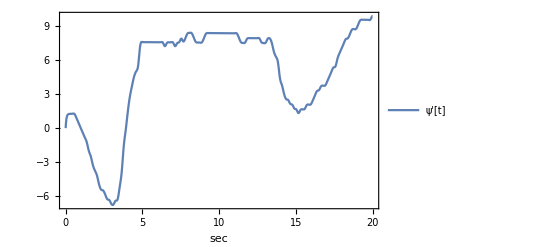

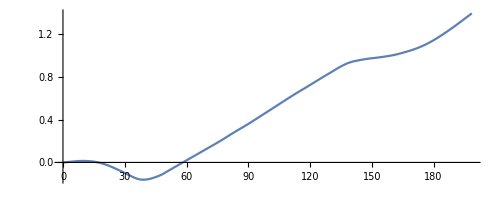

-Graphics-

-Graphics-

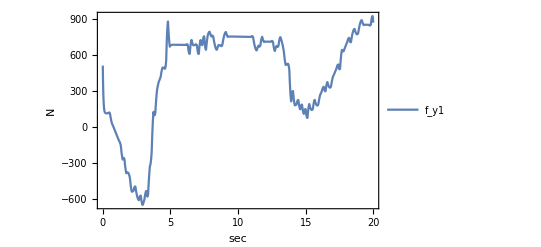

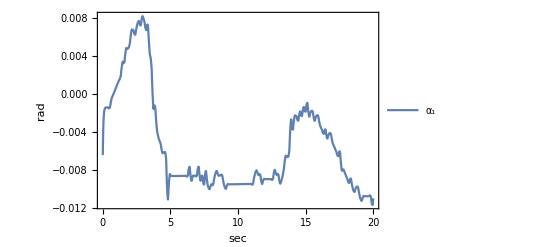

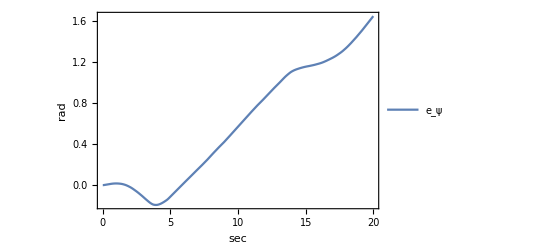

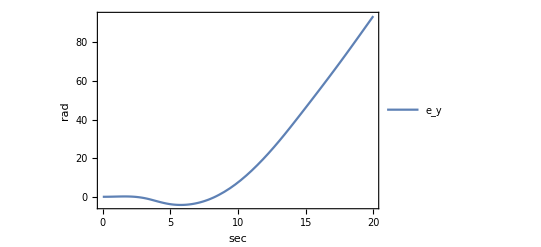

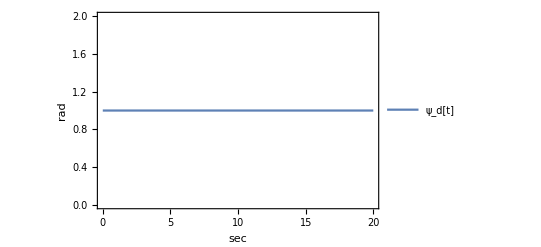

```mathematica
Brake1[t_,τ_,βr_]:=βr/2*(Tanh[20t]-Tanh[20(t-τ)]);
Brake[t_,τ0_,τ_,βr_]:=Fold[Plus,0,Table[Brake1[t-τ0⟦k⟧,τ⟦k⟧,βr⟦k⟧],{k,1,Length[τ]}]];
S1[t_,τ1_,δ1_]:=δ1/2*(Tanh[100t]-Tanh[100(t-τ1)]);
S2[t_,τ01_,τ1_,δ1_]:=Fold[Plus,0,Table[S1[t-τ01⟦k⟧,τ1⟦k⟧,δ1⟦k⟧],{k,1,Length[τ1]}]];
Subscript[β, r] = Brake[t,τ0 ,τ ,β];
η = √(1.0-Subscript[β, r]^2);
q= Import["2.dat"];
q1 = DeleteCases[Table[If[q[[k,1]] == q[[k+1,1]], null ,q[[k+1]]],{k,1,Length[q]-1}],null];
q2 = Map[({First[#]-0.2945,Last[#]})&,q1];
q3 = Interpolation[q2];
δ = q3[t];

rules =
{
Subscript[C, α1]->80000.0,Subscript[C, α2]->80000.0,Subscript[C, α3]->80000.0,Subscript[C, α4]->80000.0,
Subscript[μ, 1]->1.0,Subscript[μ, 2]->1.0,Subscript[μ, 3]->1.0,Subscript[μ, 4]->1.0,
Subscript[F, z1]->26719.0,Subscript[F, z2]->26719.0,Subscript[F, z3]->21295.0,Subscript[F, z4]->21295.0(*NOT SURE*),
m ->2050.0,Subscript[ω, t]->1.63,Subscript[l, f]->1.43,Subscript[l, r]->1.47 , Subscript[J, z] -> 3344.0 ,
Subscript[K, y]->5000,Subscript[K, ψ]-> 0,Subscript[ψ, d1] ->-0.12,Subscript[t, lp] -> 1.5
};

Slip angle;
f1[μ_,F_,C_]:=ArcTan[(3η μ F)/C]/.rules;
Subscript[α, sl1]=f1[Subscript[μ, 1],Subscript[F, z1],Subscript[C, α1]]; Subscript[α, sl2]=f1[Subscript[μ, 2],Subscript[F, z2],Subscript[C, α2]];
Subscript[α, sl3]=f1[Subscript[μ, 3],Subscript[F, z3],Subscript[C, α3]]; Subscript[α, sl4]=f1[Subscript[μ, 4],Subscript[F, z4],Subscript[C, α4]];

f2[δ_,l_]:=(y'[t] + l ψ'[t])/x'[t]-δ/.rules;
Subscript[α, 1]=f2[δ,Subscript[l, f]]; Subscript[α, 2]=f2[δ,Subscript[l, f]];
Subscript[α, 3]=f2[0,-Subscript[l, r]]; Subscript[α, 4]=f2[0,-Subscript[l, r]];

Tire  Lateral Force;
f3[C_,α_,μ_,F_,αs_]:=Piecewise[{{ - C Tan[α]+ C^2/(3η μ F) Abs[Tan[α]] Tan[α]- C^3/(27(η μ F)^2)Tan[α]^3,Abs[α]<αs},{-η μ F Sign[α],Abs[α]≥αs}}]/.rules;
Subscript[f, y1]=f3[Subscript[C, α1],Subscript[α, 1],Subscript[μ, 1],Subscript[F, z1],Subscript[α, sl1]]/.rules; Subscript[f, y2]=f3[Subscript[C, α2],Subscript[α, 2],Subscript[μ, 2],Subscript[F, z2],Subscript[α, sl2]]/.rules;
Subscript[f, y3]=f3[Subscript[C, α3],Subscript[α, 3],Subscript[μ, 3],Subscript[F, z3],Subscript[α, sl3]]/.rules; Subscript[f, y4]=f3[Subscript[C, α4],Subscript[α, 4],Subscript[μ, 4],Subscript[F, z4],Subscript[α, sl4]]/.rules;

Tire  Longitudinal Force;
f4[μ_,F_]:=Subscript[β, r] μ F/.rules;
Subscript[f, x1]=f4[Subscript[μ, 1],Subscript[F, z1]]/.rules; Subscript[f, x2]=f4[Subscript[μ, 2],Subscript[F, z2]]/.rules;
Subscript[f, x3]=f4[Subscript[μ, 3],Subscript[F, z3]]/.rules; Subscript[f, x4]=f4[Subscript[μ, 4],Subscript[F, z4]]/.rules;

Long. and Lat. Tot. Forces;
Subscript[F, x1] =Subscript[f, x1] Cos[δ] - Subscript[f, y1] Sin[δ]; Subscript[F, x2] =Subscript[f, x2] Cos[δ] - Subscript[f, y2] Sin[δ];
Subscript[F, x3] =Subscript[f, x3] Cos[0] - Subscript[f, y3] Sin[0]; Subscript[F, x4] =Subscript[f, x4] Cos[0] - Subscript[f, y4] Sin[0];

Subscript[F, y1] =Subscript[f, x1] Sin[δ] + Subscript[f, y1] Cos[δ]; Subscript[F, y2] =Subscript[f, x2] Sin[δ] + Subscript[f, y2] Cos[δ];
Subscript[F, y3] =Subscript[f, x3] Sin[0] + Subscript[f, y3] Cos[0]; Subscript[F, y4] =Subscript[f, x4] Sin[0] + Subscript[f, y4] Cos[0];

u[t] = 1;
Equations of Motion;
Eq1 = m x''[t]== m y'[t]ψ'[t] + Subscript[F, x1] +Subscript[F, x2] +Subscript[F, x3] +Subscript[F, x4];
Eq2 = m y''[t] == -m x'[t] ψ'[t] + Subscript[F, y1]+ Subscript[F, y2]+ Subscript[F, y3]+ Subscript[F, y4];
Eq3 =Subscript[J, z] ψ''[t] == Subscript[l, f](Subscript[F, y1] + Subscript[F, y2]) - Subscript[l, r](Subscript[F, y3] + Subscript[F, y4]) + (Subscript[ω, t]/2)( Subscript[F, x2] -Subscript[F, x1] - Subscript[F, x3] + Subscript[F, x4]);
Eq4 = Subscript[e, ψ]'[t]== ψ'[t]- D[u[t],t];
Eq5 = Subscript[e, y]'[t]==y'[t] Cos[Subscript[e, ψ][t]] + x'[t]Sin[Subscript[e, ψ][t]];

motionEq ={Eq1,Eq2,Eq3,Eq4,Eq5};

time =20;

τ0 = {1,10,20,50};
τ = {0.6,5,5,5};
β={0.0,0,0,0.0};
τ01 = {4,  8,            15,       62,      95 ,      100};
τ1 = {0.1,7,            25,       6,        5 ,         10};
δ1={0.02,-0.028,0.028,0.025,-0.03,0.03};

initCond={x[0]==0.1,x'[0]==10,y[0]==0.0,y'[0]==0.00,ψ[0]==0.00,ψ'[0]==0.00, Subscript[e, ψ][0] == 0, Subscript[e, y][0] == 0};
solution=NDSolve[{motionEq/.rules,initCond},{x,y,ψ,Subscript[e, ψ],Subscript[e, y]},{t,0,time}]

f5[x_,y_,l2_,s1_,s2_]:=Plot[Evaluate[{x,y}/.solution],{t,0,time},Frame->True,FrameLabel->{sec,l2},PlotLegends->{s1,s2},PlotRange->All] ;

f5[x[t],y[t],m,x[t],"y(t)"]
f5[x'[t]*3.6,y'[t]*3.6,"km/h","v_x(t)","v_y(t)"]
f5[x''[t],y''[t],"m/s^2","a_x(t)","a_y(t)"]
f5[δ,,"","δ",""]
f5[ψ'[t]*180/π,,"","ψ'[t]",""]
Plot1 = ParametricPlot[{{x[t],y[t]}/.solution},{t,0,time},PlotRange-> All]
Plot2 = ParametricPlot[{{u[t]}},{t,0,time},PlotRange-> All]
Show[{Plot1,Plot2}, PlotRange-> All]
f5[Subscript[f, y1],,"N","f_y1",""]
f5[Subscript[α, 1],,"rad","α_1",""]
f5[Subscript[e, ψ][t],,"rad","e_ψ",""]
f5[Subscript[e, y][t],,"rad","e_y",""]
f5[u[t],,"rad","ψ_d[t]",""]
```

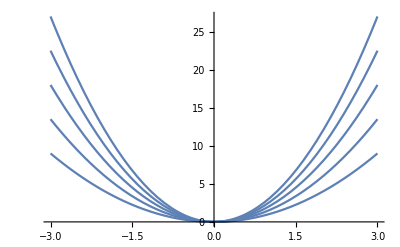

```mathematica
g[x_,y_,γ_]:=γ x^2+y
Plot3D[Table[g[x,γ],{γ,1,3,.5}],{x,-3,3},Plot]
```

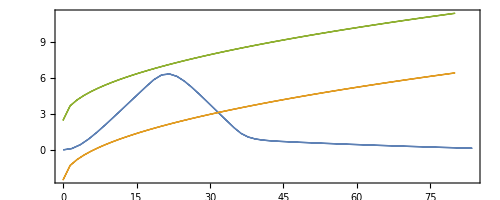

```mathematica
ParametricPlot[{{x[t],y[t]}/.solution,{z,z^(1/2)-2.5},{z,z^(1/2)+2.5}},{z,0,80},{t,0,time},PlotRange-> All]
```

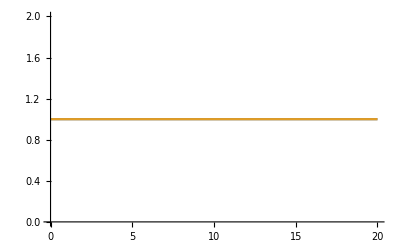

```mathematica
P2 = Plot[Evaluate[{u[t],u[t]}/.solution],{t,0,time}]
```

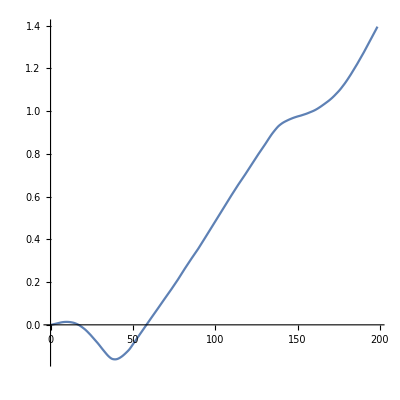

```mathematica
P1 = ParametricPlot[{x[t],y[t]}/.solution,{t,0,time},AspectRatio->1]
```

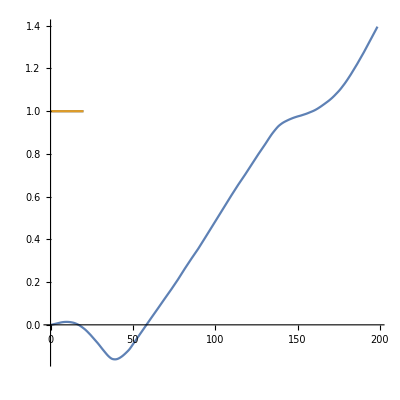

```mathematica
Show[{P1,P2},PlotRange ->All,AspectRatio-> 1]
```